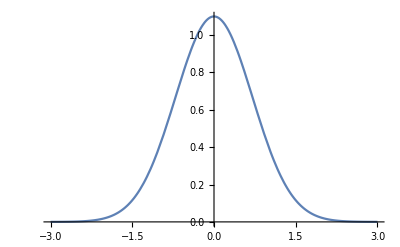

```mathematica
P=Function[{x,c},c*Exp[-x^2]];
Plot[P[x,1.1],{x,-3,3}]
```

```mathematica
CircleU[α_,ρ_]=1-P[ρ*Exp[ⅈ*ϕ],1.1]Exp[-α*Abs[y[ϕ]]^2];
CircleEq[k_,α_,ρ_]={y''[ϕ]-ⅈ*y'[ϕ]-ρ^2*Exp[2ⅈ*ϕ]k^2*CircleU[α,ρ]y[ϕ]==0,y[0]==Exp[ρ*ⅈ*k],y[2π]==Exp[ρ*ⅈ*k]};
ProgressIndicator[Dynamic[ind],{0,2π}]
CircleSol=NDSolve[CircleEq[30,0,2],y[ϕ],{ϕ,0,2π},StepMonitor:>(ind=ϕ)];
Clear[ind];
```

$Aborted

```mathematica
Plot[Re[y[ϕ]/.CircleSol],{ϕ,0,2π}]
```

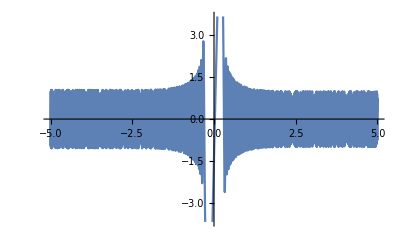

```mathematica
ReU[α_]=1-P[x,1.1]Exp[-α*Abs[y[x]]^2];
ReEq[k_,α_]={y''[x]+k^2*ReU[α]y[x]==0,y[5]==Exp[5ⅈ*k],y'[5]==ⅈ*k*Exp[5ⅈ*k]};
ProgressIndicator[Dynamic[ind],{5,-5}]
ReSol=NDSolve[ReEq[500,0.001],y[x],{x,-5,5},StepMonitor:>(ind=x)];
Plot[Re[y[x]/.ReSol],{x,-5,5}]
Clear[ind];
```

```mathematica
ImU[α_]=1-P[-ⅈ*x,1.1]Exp[-α*Abs[y[x]]^2];
ImEq[k_,α_]={y''[x]+k^2*ImU[α]y[x]==0,y[10]==Exp[10ⅈ*k],y'[10]==ⅈ*k*Exp[10ⅈ*k]};
ImSol=NDSolve[ImEq[30,0],y[x],{x,-2,2}];
Plot[Re[y[x]/.ImSol],{x,-2,2}]
```

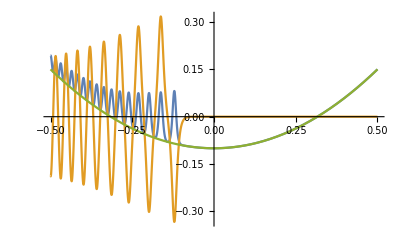

```mathematica
a=0.00000000000000000000000000000000000000000000000001;
sol=NDSolve[ReEq[500,a],y[x],{x,-5,5}];
Plot[{Re[U[a]/.sol],(Sqrt[a]*Re[y[x]/.sol]),U[0]},{x,-0.5,0.5}]
```

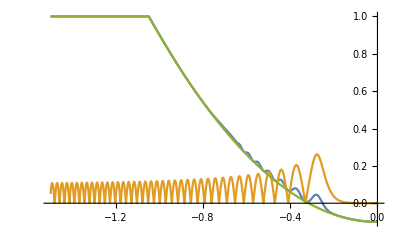

```mathematica
a=0.000000000000000000001;
sol=NDSolve[ReEq[150,a],y[x],{x,-5,5}];
Plot[{Re[U[a]/.sol],(Sqrt[a]*Abs[y[x]/.sol]),U[0]},{x,-1.5,0}]
```